```mathematica
numbers={a->1.,ν->0.07453,α->0.000002};
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

F:\Загрузки\Диплом\Diploma_Nb

```mathematica
SetOptions[{Plot,ListPlot,ListLinePlot,ListLogLinearPlot},PlotRange->Full,Axes->False,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],BaseStyle->{FontFamily->"Courier",FontSize->12, Bold},ImageSize->500,PlotStyle->{Red,PointSize[0.01]}];
```

```mathematica
NAFF[x_]:=Abs[Take[Table[Sum[x[[n]]*Exp[ⅈ*2π*β*n],{n,1,Length[x]}],{β,0,1,0.0001}],{1,5001}]]
```

```mathematica
NumPlace[x_]:=Position[NAFF[x],Max[NAFF[x]]][[1,1]]
```

```mathematica
FreqList[x_]:=Table[1.0*b/10000,{b,0,5000}]
```

```mathematica
Freq[x_]:=FreqList[x][[NumPlace[x]]]
```

```mathematica
TruePlot[x_]:=ListPlot[Transpose[{FreqList[x][[1;;5001]],NAFF[x][[1;;5001]]}],FrameLabel->{"ν","A, mm"}]
```

0% Level

```mathematica
sig0=Table[a E^(-α k^2)Sin[2 π ν k]/.numbers,{k,1,500}];
```

0.0745

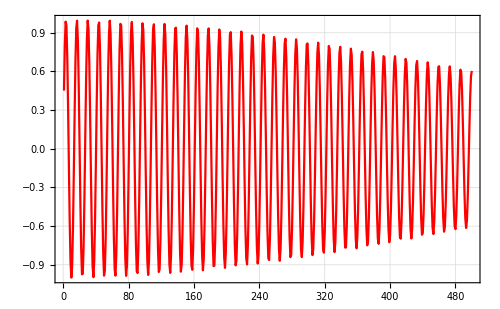

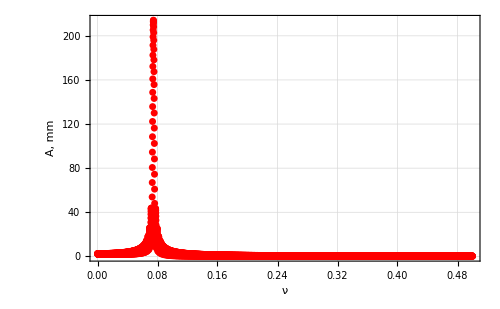

```mathematica
Freq0 =Freq[sig0]
Image0=ListLinePlot[sig0]
NAFF0=TruePlot[sig0]
```

25% Level

```mathematica
sig25=Table[0.5*(Random[]-0.5)+a E^(-α k^2)Sin[2 π ν k]/.numbers,{k,1,500}];
```

0.0745

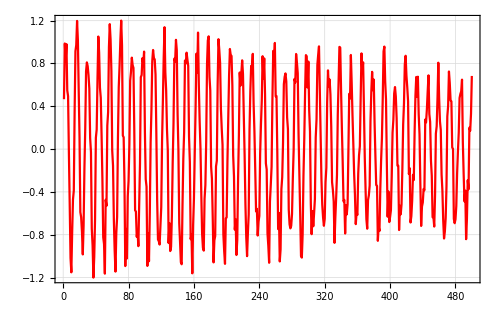

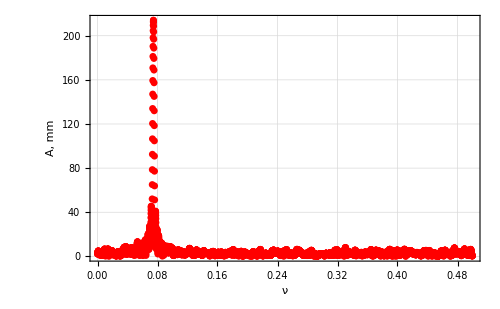

```mathematica
Freq25=Freq[sig25]
Image25=ListLinePlot[sig25]
NAFF25=TruePlot[sig25]
```

50% Level

0.0745

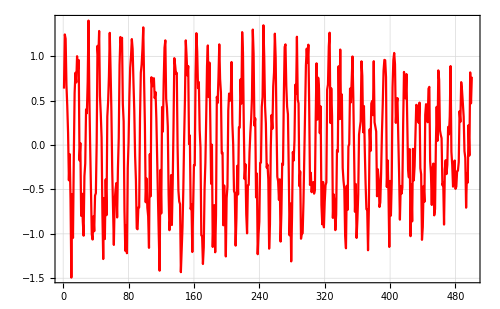

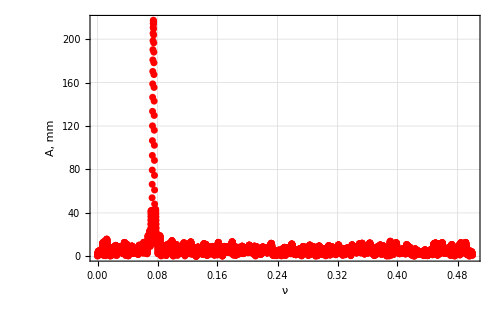

```mathematica
sig50=Table[(Random[]-0.5)+a E^(-α k^2)Sin[2 π ν k]/.numbers,{k,1,500}];
Freq50 =Freq[sig50]
Image50=ListLinePlot[sig50]
NAFF50=TruePlot[sig50]
```

75% Level

0.0745

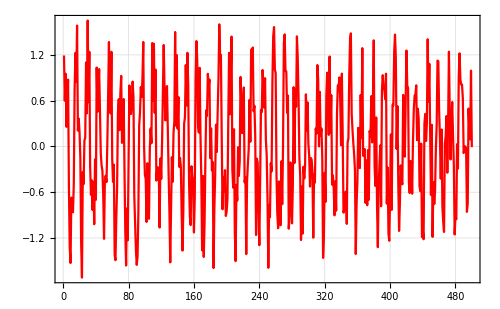

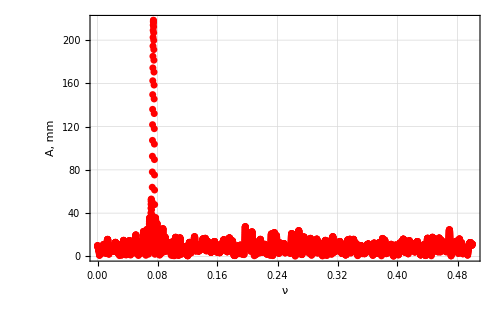

```mathematica
sig75=Table[1.5*(Random[]-0.5)+a E^(-α k^2)Sin[2 π ν k]/.numbers,{k,1,500}];
Freq75 =Freq[sig75]
Image75=ListLinePlot[sig75]
NAFF75=TruePlot[sig75]
```

100% Level

0.0745

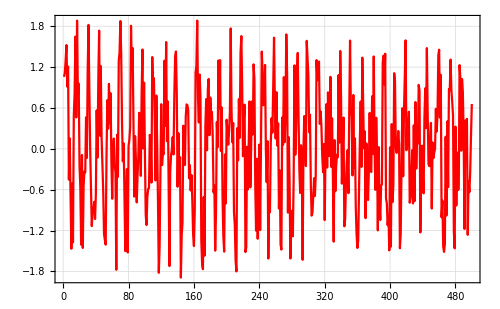

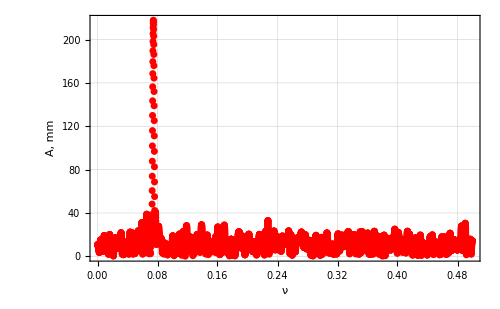

```mathematica
sig100=Table[2*(Random[]-0.5)+a E^(-α k^2)Sin[2 π ν k]/.numbers,{k,1,500}];
Freq100 =Freq[sig100]
Image100=ListLinePlot[sig100]
NAFF100=TruePlot[sig100]
```

```mathematica
depen =Transpose[{{0,25,50,75,100},{Freq0, Freq25,Freq50,Freq75,Freq100}*10^5-ν*10^5}/.numbers]
```

{{0,-3.},{25,-3.},{50,-3.},{75,-3.},{100,-3.}}

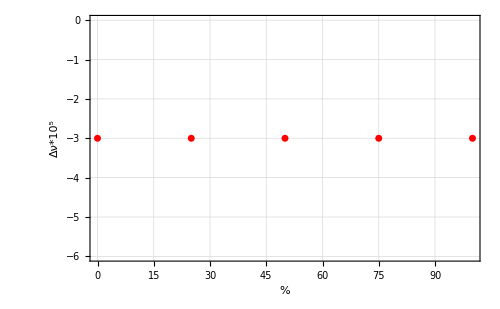

```mathematica
DeltaNAFF=ListPlot[depen,Axes->True,FrameLabel->{"%","Δν*10^5"}]
```

```mathematica
Export["DeltaNAFFNoise.png",DeltaNAFF]
```

DeltaMAFFNoise.png